Berechne Plateau...

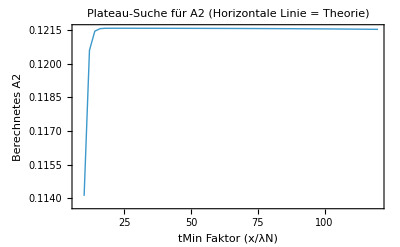

```mathematica
ClearAll["Global`*"];

(*1. Daten laden*)
path="C:/Users/sulta/git/cone-operator-lab/data/eigenvalues/box_a1.0_b1.5_c2.3_N20000.txt";
eigs=Sort@Select[Flatten@Import[path,"Table"]//N,#>0&];
λN=Last[eigs];

(*2. Parameter für die Plateau-Suche*)
(*Wir variieren den Faktor für tMin von 10 bis 100*)
tMinFactors=Range[10,120,2];
tMaxFactor=400;

calculateA2[fMin_]:=Module[{tMin,tMax,tGrid,Z,X,coef,α2,a2hat},tMin=fMin/λN;
tMax=tMaxFactor/λN;
tGrid=Exp@Subdivide[Log[tMin],Log[tMax],150];
Z=Total[Exp[-Outer[Times,eigs,tGrid]],{1}];
X=Table[t^{-3/2,-1,-1/2,0},{t,tGrid}];
coef=PseudoInverse[X].Z;
α2=coef[[3]];
(*Umrechnung zu A2*)a2hat=(α2*(4 Pi)^(3/2))/(4 Pi^3)];

Print["Berechne Plateau..."];
results=Table[{f,calculateA2[f]},{f,tMinFactors}];

(*3. Visualisierung*)
A2true=(Pi (1.0+1.5+2.3))/(12 Pi^2);

ListLinePlot[results,GridLines->{None,{A2true}},PlotStyle->Thick,PlotRange->All,Frame->True,FrameLabel->{"tMin Faktor (x/λN)","Berechnetes A2"},PlotLabel->"Plateau-Suche für A2 (Horizontale Linie = Theorie)",Epilog->{Red,Dashed,InfiniteLine[{0,A2true},{1,0}]}]
```